```mathematica
(*g={0.0000001593,0.0000001266,0.0000001365};
o={0.88,0.13,0.38};*)
g={1};
o={1};
n=Length[g];
f[x_,v_]:=Gamma[(v+1)/2]((1+x^2/v)^(-(v+1)/2))/(Sqrt[v Pi]Gamma[v/2]);
lnf[x_,v_]:=Log[f[x,v]];
dlnf[x_,v_]:=D[lnf[x,v],v];
q[v_]:=(Log[v]+2 Gamma[(v+1)/2]-2 Gamma[v/2])Sum[g[[i]],{i,n}]+Sum[g[[i]]((o[[i]]^2-1)/(o[[i]]^2+v)-Log[o[[i]]^2+v]),{i,n}];
dq[v_]:=(1/v+PolyGamma[1,(v+1)/2]-PolyGamma[1,v/2])Sum[g[[i]],{i,n}]+Sum[g[[i]](2 o[[i]]^2-1+v)/((o[[i]]^2+v)^2),{i,n}];
```

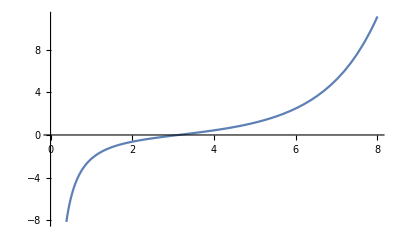

```mathematica
Plot[q[v],{v,0,8}]
```

```mathematica
FindRoot[q[v],{v,3}]
```

{v→3.12758}

```mathematica
newton[v0_]:=v0-q[v0]/dq[v0];
NestList[newton,3,6]//N
```

{3.,3.20492,3.0835,3.15345,3.11269,3.13624,3.12258}